## Paquetes y definiciones para este cuaderno

```mathematica
(* Set directory to this notebook's directory *)
SetDirectory[NotebookDirectory[]];
Get["../Mathematica_packages/QMB.wl"]
```

```mathematica
(* Operador de evolución *)
U[H_,t_]:=MatrixExp[-I*H*t]
```

## Cosas que tenía de la primera vez que cree este cuaderno

```mathematica
L=3;H=IsingNNOpenHamiltonian[1.,0.5,1.,L];
```

```mathematica
ψ=RandomChainProductState[L-1];ϕ={1,0};
```

```mathematica
KroneckerProduct[Pauli[0],Dyad[RandomChainProductState[4]]]
```

SparseArray[…]

```mathematica
MatrixPartialTrace[#.(KroneckerProduct[Pauli[0]/2,Dyad[ψ]]).ConjugateTranspose[#]&[MatrixExp[-I H]],1,2]//Purity
```

0.513876+3.50141×10^-18 ⅈ

```mathematica
Purity[MatrixPartialTrace[#.Dyad[KroneckerVectorProduct[ϕ,ψ]].ConjugateTranspose[#]&[MatrixExp[-I H]],Range[2,L],2]]
```

0.589828-1.00662×10^-17 ⅈ

```mathematica
(*2da línea*)
Tr[(KroneckerProduct[#,#]&[MatrixPartialTrace[#.Dyad[KroneckerVectorProduct[ϕ,ψ]].ConjugateTranspose[#]&[MatrixExp[-I H]],Range[2,L],2]]).PermutationMatrix[{1,3,2,4}]]
```

0.589828-1.00662×10^-17 ⅈ

```mathematica
(*4ta línea*)
Tr[(KroneckerProduct[#,#].KroneckerProduct[Dyad[KroneckerVectorProduct[ϕ,ψ]],Dyad[KroneckerVectorProduct[ϕ,ψ]]].KroneckerProduct[ConjugateTranspose[#],ConjugateTranspose[#]]&[MatrixExp[-I H]]).PermutationMatrix[{1,2,3,4,33,34,35,36,9,10,11,12,41,42,43,44,17,18,19,20,49,50,51,52,25,26,27,28,57,58,59,60,5,6,7,8,37,38,39,40,13,14,15,16,45,46,47,48,21,22,23,24,53,54,55,56,29,30,31,32,61,62,63,64}]]
```

0.589828+1.94614×10^-17 ⅈ

```mathematica
(*6ta línea*)
Tr[(KroneckerProduct[#,#].PermutationMatrix[{1,2,3,4,17,18,19,20,5,6,7,8,21,22,23,24,9,10,11,12,25,26,27,28,13,14,15,16,29,30,31,32,33,34,35,36,49,50,51,52,37,38,39,40,53,54,55,56,41,42,43,44,57,58,59,60,45,46,47,48,61,62,63,64}].Dyad[Flatten[KroneckerProduct[ϕ,ϕ,ψ,ψ]]].ConjugateTranspose[PermutationMatrix[{1,2,3,4,17,18,19,20,5,6,7,8,21,22,23,24,9,10,11,12,25,26,27,28,13,14,15,16,29,30,31,32,33,34,35,36,49,50,51,52,37,38,39,40,53,54,55,56,41,42,43,44,57,58,59,60,45,46,47,48,61,62,63,64}]].KroneckerProduct[ConjugateTranspose[#],ConjugateTranspose[#]]&[MatrixExp[-I H]]).PermutationMatrix[{1,2,3,4,33,34,35,36,9,10,11,12,41,42,43,44,17,18,19,20,49,50,51,52,25,26,27,28,57,58,59,60,5,6,7,8,37,38,39,40,13,14,15,16,45,46,47,48,21,22,23,24,53,54,55,56,29,30,31,32,61,62,63,64}]]
```

0.589828+5.74627×10^-18 ⅈ

```mathematica
PermutationMatrix[{1,2,3,4,17,18,19,20,5,6,7,8,21,22,23,24,9,10,11,12,25,26,27,28,13,14,15,16,29,30,31,32,33,34,35,36,49,50,51,52,37,38,39,40,53,54,55,56,41,42,43,44,57,58,59,60,45,46,47,48,61,62,63,64}].Pauli[{1,1,0,0,0,0}].ConjugateTranspose[PermutationMatrix[{1,2,3,4,17,18,19,20,5,6,7,8,21,22,23,24,9,10,11,12,25,26,27,28,13,14,15,16,29,30,31,32,33,34,35,36,49,50,51,52,37,38,39,40,53,54,55,56,41,42,43,44,57,58,59,60,45,46,47,48,61,62,63,64}]]==Pauli[{1,0,0,1,0,0}]
```

True

```mathematica
Tr[(KroneckerProduct[#,#]&[#.Dyad[KroneckerVectorProduct[ϕ,ψ]].ConjugateTranspose[#]&[MatrixExp[-I H]]]).PermutationMatrix[{1,2,3,4,33,34,35,36,9,10,11,12,41,42,43,44,17,18,19,20,49,50,51,52,25,26,27,28,57,58,59,60,5,6,7,8,37,38,39,40,13,14,15,16,45,46,47,48,21,22,23,24,53,54,55,56,29,30,31,32,61,62,63,64}]]
```

```mathematica
ψ=Normalize[{1.,0,0,1.}];
```

```mathematica
Purity[MatrixPartialTrace[Dyad[ψ],2,2]]
```

0.5

```mathematica
Tr[KroneckerProduct[MatrixPartialTrace[Dyad[ψ],2,2],MatrixPartialTrace[Dyad[ψ],2,2]].PermutationMatrix[{1,3,2,4}]]
```

0.5

```mathematica
Tr[KroneckerProduct[Dyad[ψ],Dyad[ψ]].PermutationMatrix[{1,2,9,10,5,6,13,14,3,4,11,12,7,8,15,16}]]
```

0.5

```mathematica
KetInComputationalBasisFromVector[KroneckerProduct[Pauli[1],Pauli[0],Pauli[1],Pauli[0]].VectorFromKetInComputationalBasis[{1,1,0,1}]]
```

{0,1,1,1}

```mathematica
KetInComputationalBasisFromVector[PermutationMatrix[{1,3,2,4}].VectorFromKetInComputationalBasis[{0,1}]]
```

{1,0}

```mathematica
Flatten[Position[Tuples[{0,1},2L],{#[[1]],#[[4]],#[[2]],#[[3]],#[[5]],#[[6]]}]&/@Tuples[{0,1},2L]]
```

{1,2,3,4,17,18,19,20,5,6,7,8,21,22,23,24,9,10,11,12,25,26,27,28,13,14,15,16,29,30,31,32,33,34,35,36,49,50,51,52,37,38,39,40,53,54,55,56,41,42,43,44,57,58,59,60,45,46,47,48,61,62,63,64}

```mathematica
KetInComputationalBasisFromVector[PermutationMatrix[{1,2,9,10,5,6,13,14,3,4,11,12,7,8,15,16}].VectorFromKetInComputationalBasis[{0,0,1,0}]]
```

{1,0,0,0}

```mathematica
Tuples[{0,1},2L]//Length
```

64

## Average Choi purity

```mathematica
Chop[(1/48)3Purity[MatrixPartialTrace[#.Pauli[{0,0,0}].ConjugateTranspose[#]&[MatrixExp[-I H]],1,2]]]
```

1.

```mathematica
Chop[MatrixPartialTrace[#.Pauli[{0,0,0}].ConjugateTranspose[#]&[MatrixExp[-I H]],1,2]]
```

{{2.,0,0,0},{0,2.,0,0},{0,0,2.,0},{0,0,0,2.}}

```mathematica
Chop[(1/48)3Purity[MatrixPartialTrace[#.Pauli[{0,2,1}].ConjugateTranspose[#]&[MatrixExp[-I H]],1,2]]]
```

0.483052

```mathematica
t=100.2;Chop[(1/4)Purity[MatrixPartialTrace[#.(KroneckerProduct[Pauli[0],Dyad[ψ]]).ConjugateTranspose[#]&[MatrixExp[-I H t]],1,2]]]
```

0.388717

```mathematica
t=10;1/4Tr[(KroneckerProduct[#,#].PermutationMatrix[{1,2,9,10,17,18,25,26,3,4,11,12,19,20,27,28,5,6,13,14,21,22,29,30,7,8,15,16,23,24,31,32,33,34,41,42,49,50,57,58,35,36,43,44,51,52,59,60,37,38,45,46,53,54,61,62,39,40,47,48,55,56,63,64}].KroneckerProduct[IdentityMatrix[4],(1/6(Pauli[{0,0}]+PermutationMatrix[{1,3,2,4}])),(1/6(Pauli[{0,0}]+PermutationMatrix[{1,3,2,4}]))].ConjugateTranspose[PermutationMatrix[{1,2,9,10,17,18,25,26,3,4,11,12,19,20,27,28,5,6,13,14,21,22,29,30,7,8,15,16,23,24,31,32,33,34,41,42,49,50,57,58,35,36,43,44,51,52,59,60,37,38,45,46,53,54,61,62,39,40,47,48,55,56,63,64}]].KroneckerProduct[ConjugateTranspose[#],ConjugateTranspose[#]]&[MatrixExp[-I H t]]).PermutationMatrix[{1,2,3,4,33,34,35,36,9,10,11,12,41,42,43,44,17,18,19,20,49,50,51,52,25,26,27,28,57,58,59,60,5,6,7,8,37,38,39,40,13,14,15,16,45,46,47,48,21,22,23,24,53,54,55,56,29,30,31,32,61,62,63,64}]]
```

0.659709+2.1684×10^-19 ⅈ

```mathematica
Flatten[Position[Tuples[{0,1},2L],{#[[1]],#[[4]],#[[5]],#[[2]],#[[3]],#[[6]]}]&/@Tuples[{0,1},2L]]
```

{1,2,9,10,17,18,25,26,3,4,11,12,19,20,27,28,5,6,13,14,21,22,29,30,7,8,15,16,23,24,31,32,33,34,41,42,49,50,57,58,35,36,43,44,51,52,59,60,37,38,45,46,53,54,61,62,39,40,47,48,55,56,63,64}

## Revisando los cálculos de mi cuaderno

Cargar variables:

```mathematica
(* Número de espines *)
L=3;

(* Hamiltoniano de Ising (cadena de Wisniacki) *)
H=IsingNNOpenHamiltonian[1.,0.5,1.,L];

(* Estado inicial del entorno *)
ψ=RandomChainProductState[L-1];
```

```mathematica
Chop[Purity[MatrixPartialTrace[#.(KroneckerProduct[Pauli[0]/2,Dyad[ψ]]).ConjugateTranspose[#]&[MatrixExp[-I H]],1,2]]]
```

0.758603

```mathematica
p=Flatten[Position[Tuples[{0,1},2L],{#[[1]],#[[5]],#[[6]],#[[4]],#[[2]],#[[3]]}]&/@Tuples[{0,1},2L]]
```

{1,9,17,25,5,13,21,29,2,10,18,26,6,14,22,30,3,11,19,27,7,15,23,31,4,12,20,28,8,16,24,32,33,41,49,57,37,45,53,61,34,42,50,58,38,46,54,62,35,43,51,59,39,47,55,63,36,44,52,60,40,48,56,64}

```mathematica
KetInComputationalBasisFromVector[PermutationMatrix[p].VectorFromKetInComputationalBasis[{1,0,0,0,1,1}]]
KetInComputationalBasisFromVector[PermutationMatrix[p].VectorFromKetInComputationalBasis[{0,0,1,1,1,0}]]
```

{1,1,1,0,0,0}

{0,1,0,1,0,1}

```mathematica
Chop[Tr[KroneckerProduct[#.KroneckerProduct[Pauli[0]/2,Dyad[ψ]].ConjugateTranspose[#],#.KroneckerProduct[Pauli[0]/2,Dyad[ψ]].ConjugateTranspose[#]]&[MatrixExp[-I H]].PermutationMatrix[p]]]
```

0.758603

```mathematica
Chop[Tr[KroneckerProduct[#,#].KroneckerProduct[KroneckerProduct[Pauli[0]/2,Dyad[ψ]],KroneckerProduct[Pauli[0]/2,Dyad[ψ]]].KroneckerProduct[ConjugateTranspose[#],ConjugateTranspose[#]]&[MatrixExp[-I H]].PermutationMatrix[p]]]
```

0.758603

Matriz de permutación

```mathematica
p2=Flatten[Position[Tuples[{0,1},2L],{#[[1]],#[[4]],#[[2]],#[[5]],#[[3]],#[[6]]}]&/@Tuples[{0,1},2L]]
```

{1,2,5,6,17,18,21,22,3,4,7,8,19,20,23,24,9,10,13,14,25,26,29,30,11,12,15,16,27,28,31,32,33,34,37,38,49,50,53,54,35,36,39,40,51,52,55,56,41,42,45,46,57,58,61,62,43,44,47,48,59,60,63,64}

```mathematica
(* Calcular cómo se transfomar un estado □*)
Total[Table[i*KetInComputationalBasisFromVector[PermutationMatrix[p2].VectorFromKetInComputationalBasis[SparseArray[i->1,2L]]],{i,2L}]]
```

{1,3,5,2,4,6}

El estado inicial del entorno es de la forma: ψ=ψ_1⊗ψ_2

```mathematica
(* Estados ψ1 y ψ2 *)
{ψ1,ψ2}=Eigensystem[MatrixPartialTrace[Dyad[ψ],#,2]][[2,1]]&/@{2,1}
```

{{0.523324-0.703263 ⅈ,0.481199+0. ⅈ},{-0.299628-0.191653 ⅈ,0.934608+0. ⅈ}}

```mathematica
MatrixForm/@{KroneckerProduct[Dyad[ψ1],Dyad[ψ2]],Dyad[ψ]}
```

{(0.150961+0. ⅈ | -0.0787104-0.109918 ⅈ | 0.116128+0.217942 ⅈ | 0.0981396-0.198189 ⅈ
-0.0787104+0.109918 ⅈ | 0.121073+0. ⅈ | -0.219236-0.0290792 ⅈ | 0.0931356+0.174792 ⅈ
0.116128-0.217942 ⅈ | -0.219236+0.0290792 ⅈ | 0.403974+0. ⅈ | -0.21063-0.294142 ⅈ
0.0981396+0.198189 ⅈ | 0.0931356-0.174792 ⅈ | -0.21063+0.294142 ⅈ | 0.323992+0. ⅈ),(0.150961+0. ⅈ | -0.0787104-0.109918 ⅈ | 0.116128+0.217942 ⅈ | 0.0981396-0.198189 ⅈ
-0.0787104+0.109918 ⅈ | 0.121073+0. ⅈ | -0.219236-0.0290792 ⅈ | 0.0931356+0.174792 ⅈ
0.116128-0.217942 ⅈ | -0.219236+0.0290792 ⅈ | 0.403974+0. ⅈ | -0.21063-0.294142 ⅈ
0.0981396+0.198189 ⅈ | 0.0931356-0.174792 ⅈ | -0.21063+0.294142 ⅈ | 0.323992+0. ⅈ)}

```mathematica
Chop[Tr[KroneckerProduct[#,#].KroneckerProduct[Pauli[0]/2,Dyad[ψ1],Dyad[ψ2],Pauli[0]/2,Dyad[ψ1],Dyad[ψ2]].KroneckerProduct[ConjugateTranspose[#],ConjugateTranspose[#]]&[MatrixExp[-I H]].PermutationMatrix[p]]]
```

0.758603

```mathematica
Chop[Tr[KroneckerProduct[#,#].PermutationMatrix[p2].KroneckerProduct[Pauli[0]/2,Pauli[0]/2,Dyad[ψ1],Dyad[ψ1],Dyad[ψ2],Dyad[ψ2]].ConjugateTranspose[PermutationMatrix[p2]].KroneckerProduct[ConjugateTranspose[#],ConjugateTranspose[#]]&[MatrixExp[-I H]].PermutationMatrix[p]]]
```

0.758603

```mathematica
(* Proyector al subespacio simétrico de ℂ^2⊗ℂ^2 *)
MatrixForm[Psym=#/Tr[#]&[IdentityMatrix[4]+PermutationMatrix[{1,3,2,4}]]]
```

(1/3 | 0 | 0 | 0
0 | 1/6 | 1/6 | 0
0 | 1/6 | 1/6 | 0
0 | 0 | 0 | 1/3)

```mathematica
(* Proyector al espacio simétrico en la base de Pauli strings *)
MatrixForm[PsymPaulis=1/12(3Pauli[{0,0}]+Pauli[{1,1}]+Pauli[{2,2}]+Pauli[{3,3}])]
```

(1/3 | 0 | 0 | 0
0 | 1/6 | 1/6 | 0
0 | 1/6 | 1/6 | 0
0 | 0 | 0 | 1/3)

```mathematica
PermutationMatrix[p2].KroneckerProduct[Pauli[0]/2,Pauli[0]/2,Psym,Psym].ConjugateTranspose[PermutationMatrix[p2]]
```

SparseArray[…]

```mathematica
i=2;PermutationMatrix[p2].Pauli[{0,0,i,i,0,0}].ConjugateTranspose[PermutationMatrix[p2]]==Pauli[{0,i,0,0,i,0}]
Pauli[{0,i,0,0,i,0}]==KroneckerProduct[Pauli[{0,i,0}],Pauli[{0,i,0}]]
```

True

True

```mathematica
i=2;PermutationMatrix[p2].Pauli[{0,0,0,0,i,i}].ConjugateTranspose[PermutationMatrix[p2]]==Pauli[{0,0,i,0,0,i}]
Pauli[{0,0,i,0,0,i}]==KroneckerProduct[Pauli[{0,0,i}],Pauli[{0,0,i}]]
```

True

True

```mathematica
KroneckerProduct[Pauli[0]/2,Pauli[0]/2,Psym,Psym]==(1/4)(1/12)^2(9Pauli[{0,0,0,0,0,0}]+3Sum[Pauli[{0,0,i,i,0,0}]+Pauli[{0,0,0,0,i,i}],{i,3}]+Sum[Pauli[{0,0,i,i,j,j}],{i,3},{j,3}])
```

True

```mathematica
PermutationMatrix[p2].KroneckerProduct[Pauli[0]/2,Pauli[0]/2,Psym,Psym].ConjugateTranspose[PermutationMatrix[p2]]==(1/4)(1/12)^2(9Pauli[{0,0,0,0,0,0}]+3Sum[Pauli[{0,i,0,0,i,0}]+Pauli[{0,0,i,0,0,i}],{i,3}]+Sum[Pauli[{0,i,j,0,i,j}],{i,3},{j,3}])
```

True

```mathematica
Chop[Tr[(1/4)(1/12)^2*KroneckerProduct[#,#].(9Pauli[{0,0,0,0,0,0}]+3Sum[Pauli[{0,i,0,0,i,0}]+Pauli[{0,0,i,0,0,i}],{i,3}]+Sum[Pauli[{0,i,j,0,i,j}],{i,3},{j,3}]).KroneckerProduct[ConjugateTranspose[#],ConjugateTranspose[#]]&[MatrixExp[-I H]].PermutationMatrix[p]]]
```

0.584179

```mathematica
(1/4)(1/12)^2Chop[Tr[KroneckerProduct[#,#].(9Pauli[{0,0,0,0,0,0}]+3Sum[Pauli[{0,i,0,0,i,0}]+Pauli[{0,0,i,0,0,i}],{i,3}]+Sum[Pauli[{0,i,j,0,i,j}],{i,3},{j,3}]).KroneckerProduct[ConjugateTranspose[#],ConjugateTranspose[#]]&[MatrixExp[-I H]].PermutationMatrix[p]]]
```

0.584179

```mathematica
(1/4)(1/12)^2*(9Pauli[{0,0,0}]+3Sum[Pauli[{0,i,0}]+Pauli[{0,0,i}],{i,3}]+Sum[Pauli[{0,i,j}],{i,3},{j,3}])//Tr
```

1/8

```mathematica
(1/2)(1/12)*(3Pauli[{0,0,0}]+√3 Sum[Pauli[{0,i,0}]+Pauli[{0,0,i}],{i,3}]+Sum[Pauli[{0,i,j}],{i,3},{j,3}])//Tr//FullSimplify
```

1

```mathematica
(1/2)(1/12)*#.(3Pauli[{0,0,0}]+√3 Sum[Pauli[{0,i,0}]+Pauli[{0,0,i}],{i,3}]+Sum[Pauli[{0,i,j}],{i,3},{j,3}]).ConjugateTranspose[#]&[MatrixExp[-I H]]//Tr//Chop
```

1.

```mathematica
MatrixPartialTrace[(1/2)(1/12)*#.(3Pauli[{0,0,0}]+√3 Sum[Pauli[{0,i,0}]+Pauli[{0,0,i}],{i,3}]+Sum[Pauli[{0,i,j}],{i,3},{j,3}]).ConjugateTranspose[#]&[MatrixExp[-I H]],1,2]//Chop//MatrixForm
```

(0.248109 | 0.0471468+0.279781 ⅈ | -0.0337693+0.114556 ⅈ | -0.0602761+0.0650339 ⅈ
0.0471468-0.279781 ⅈ | 0.331396 | 0.155123+0.0650245 ⅈ | 0.0811189+0.0868982 ⅈ
-0.0337693-0.114556 ⅈ | 0.155123-0.0650245 ⅈ | 0.291452 | 0.186074+0.0417339 ⅈ
-0.0602761-0.0650339 ⅈ | 0.0811189-0.0868982 ⅈ | 0.186074-0.0417339 ⅈ | 0.129043)

```mathematica
Join[3{Pauli[{0,0,0}]},√3 Flatten[Table[{Pauli[{0,i,0}],Pauli[{0,0,i}]},{i,3}],1],Flatten[Table[Pauli[{0,i,j}],{i,3},{j,3}],1]]
```

{SparseArray[…],SparseArray[…],SparseArray[…],SparseArray[…],SparseArray[…],SparseArray[…],SparseArray[…],SparseArray[…],SparseArray[…],SparseArray[…],SparseArray[…],SparseArray[…],SparseArray[…],SparseArray[…],SparseArray[…],SparseArray[…]}

```mathematica
t=1;Chop[Total[(1/2)^2*(1/12)^2*Purity[MatrixPartialTrace[U[H,t].#.ConjugateTranspose[U[H,t]],1,2]]&/@Join[3{Pauli[{0,0,0}]},√3 Flatten[Table[{Pauli[{0,i,0}],Pauli[{0,0,i}]},{i,3}],1],Flatten[Table[Pauli[{0,i,j}],{i,3},{j,3}],1]]]]
```

0.584179

```mathematica
choiPurity=Table[
{t,Chop[Total[(1/2)^2*(1/12)^2*Purity[MatrixPartialTrace[U[H,t].#.ConjugateTranspose[U[H,t]],1,2]]&/@Join[3{Pauli[{0,0,0}]},√3 Flatten[Table[{Pauli[{0,i,0}],Pauli[{0,0,i}]},{i,3}],1],Flatten[Table[Pauli[{0,i,j}],{i,3},{j,3}],1]]]]}
,{t,0,25,0.1}];
```

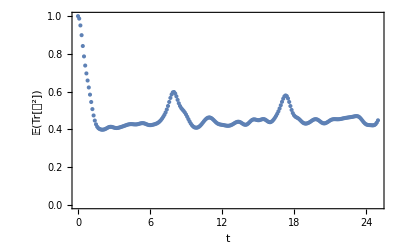

```mathematica
ListPlot[choiPurity,
PlotRange->All,
Frame->True,
FrameLabel->{TraditionalForm[HoldForm[t]],TraditionalForm[HoldForm[𝔼[Tr[𝒟^2]]]]},
FrameStyle->Directive[Black,FontSize->18]
]
```

```mathematica
TraditionalForm[HoldForm[𝔼[Tr[𝒟^2]]]]
```

𝔼(Tr[𝒟^2])

```mathematica
√27
```

3 √3

```mathematica
Sqrt[Power[3,(L-1)-Count[#,x_/;x!=0]]]*Pauli[Join[{0},#]]&/@Tuples[Range[0,3],2]
```

{SparseArray[…],SparseArray[…],SparseArray[…],SparseArray[…],SparseArray[…],SparseArray[…],SparseArray[…],SparseArray[…],SparseArray[…],SparseArray[…],SparseArray[…],SparseArray[…],SparseArray[…],SparseArray[…],SparseArray[…],SparseArray[…]}

```mathematica
t=1;Chop[Total[(1/2)^2*(1/12)^2*Purity[MatrixPartialTrace[U[H,t].#.ConjugateTranspose[U[H,t]],1,2]]&/@(Sqrt[Power[3,(L-1)-Count[#,x_/;x!=0]]]*Pauli[Join[{0},#]]&/@Tuples[Range[0,3],L-1])]]
```

0.584179

```mathematica
t=10;L=5;

(* Hamiltoniano de Ising (cadena de Wisniacki) *)
H=IsingNNOpenHamiltonian[1.,0.5,1.,L];

choiPurity=Table[
{t,
Chop[Total[(1/2)^2*(1/12)^(L-1)*Purity[MatrixPartialTrace[U[H,t].(Sqrt[Power[3,(L-1)-Count[#,x_/;x!=0]]]*Pauli[Join[{0},#]]).ConjugateTranspose[U[H,t]],1,2]]&/@Tuples[Range[0,3],L-1]]]}
,{t,0,25,0.1}];
```

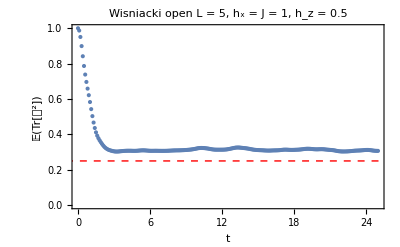

```mathematica
ListPlot[choiPurity,
PlotRange->All,
Frame->True,
FrameLabel->{TraditionalForm[HoldForm[t]],TraditionalForm[HoldForm[𝔼[Tr[𝒟^2]]]]},
FrameStyle->Directive[Black,FontSize->18],
PlotLabel->"Wisniacki open\n L = 5, h_x = J = 1, h_z = 0.5",
LabelStyle->Directive[Black,FontSize->18],
ImageSize->400,
Epilog->{Red,Dashed,Line[{{-1,0.25},{30,0.25}}]}
]
```

## Estaba verificando algunas cosas durante la reunión mar 12 nov

```mathematica
Purity[MatrixPartialTrace[IdentityMatrix[8],1,2]]
```

16

```mathematica
16*9
```

144

```mathematica
Purity[Chop[MatrixPartialTrace[#.Pauli[{0,0,0}].ConjugateTranspose[#]&[MatrixExp[-I H]],1,2]]]
```

16.

```mathematica
(1/4)*(1/12)^2*9*Purity[Chop[MatrixPartialTrace[#.Pauli[{0,0,0}].ConjugateTranspose[#]&[MatrixExp[-I H]],1,2]]]
```

0.25

```mathematica
(1/4)*(1/12)^2*Table[3Chop[Purity[MatrixPartialTrace[#.Pauli[{0,i,0}].ConjugateTranspose[#]&[MatrixExp[-I H]],1,2]]],{i,3}]
```

{0.0178406,0.0261617,0.0199616}

```mathematica
(1/4)*(1/12)^2*Table[3Chop[Purity[MatrixPartialTrace[#.Pauli[{0,0,j}].ConjugateTranspose[#]&[MatrixExp[-I H]],1,2]]],{j,3}]
```

{0.0516206,0.0607559,0.0728274}

```mathematica
(1/4)*(1/12)^2*Table[Chop[Purity[MatrixPartialTrace[#.Pauli[{0,i,j}].ConjugateTranspose[#]&[MatrixExp[-I H]],1,2]]],{i,3},{j,3}]
```

{{0.00250061,0.00320491,0.00511458},{0.0134181,0.0120839,0.0101573},{0.01584,0.0133704,0.00932112}}